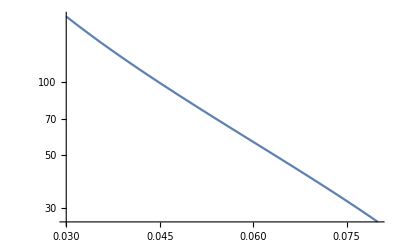

18.6227

1.47102×10^6

0.00312423

0.0542019

41.0299

0.807338

```mathematica
Clear["Global`*"]
SetOptions[Plot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];
SetOptions[LogPlot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];
SetOptions[LogLinearPlot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];
SetOptions[ContourPlot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];

Mn = 0.9383;
Md = 1.8756;
conv = 0.197327;

MELEC = 0.000510999;
MMUON = 0.105658;
hbarc = 0.197327;
ALPHAEM = 1/137.036;

eta[Qsqr_]:= Qsqr / (2. * Md)^2

a1  = 1.57057 * conv^2;
a2  = 12.23792 * conv^2;
a3  = -42.04576 * conv^2;
a4  = 27.92014 * conv^2;
als1 = 1.52501 * conv^2;
als2 = 8.75139 * conv^2;
als3 = 15.97777 * conv^2;
als4 = 23.20415 * conv^2;
g0[Qsqr_]:= a1/(als1 + Qsqr) + a2/(als2 + Qsqr) + a3/(als3 + Qsqr) + a4/(als4 + Qsqr) 
b1  = 0.07043 * conv;
b2  = 0.14443 * conv;
b3  = -0.27343 * conv;
b4  = 0.05856 * conv;
bes1 = 43.67795 * conv^2;
bes2 = 30.05435 * conv^2;
bes3 = 16.43075 * conv^2;
bes4 = 2.80716 * conv^2;
g1[Qsqr_]:= Sqrt[Qsqr] * (b1/(bes1 + Qsqr) + b2/(bes2 + Qsqr) + b3/(bes3 + Qsqr) + b4/(bes4 + Qsqr)) 
c1  = -0.16577;
c2  = 0.27557;
c3  = -0.05382 ;
c4  = -0.05598;
gas1 = 1.87055 * conv^2;
gas2 = 14.95683 * conv^2;
gas3 = 28.04312 * conv^2;
gas4 = 41.12940 * conv^2;
g2[Qsqr_]:= Qsqr * (c1/(gas1 + Qsqr) + c2/(gas2 + Qsqr) + c3/(gas3 + Qsqr) + c4/(gas4 + Qsqr)) 

GC2[Qsqr_]:= 1 / (1 + Qsqr/4/0.807)^4/(2 eta[Qsqr] + 1) * ((1-2/3 eta[Qsqr]) g0[Qsqr] + 8/3 Sqrt[2 eta[Qsqr]] g1[Qsqr] + 2/3 (2 eta[Qsqr] - 1) g2[Qsqr])
GQ2[Qsqr_]:= 1 / (1 + Qsqr/4/0.807)^4/(2 eta[Qsqr] + 1) * (- g0[Qsqr] + Sqrt[2/eta[Qsqr]] g1[Qsqr] - (eta[Qsqr] + 1)/eta[Qsqr] g2[Qsqr])
GM2[Qsqr_]:= 1 / (1 + Qsqr/4/0.807)^4/(2 eta[Qsqr] + 1) * (2 g0[Qsqr] + 2(2 eta[Qsqr] - 1) / Sqrt[2 eta[Qsqr]] g1[Qsqr] -2 g2[Qsqr])
GC[Qsqr_]:= GC2[Qsqr]
GQ[Qsqr_]:= GQ2[Qsqr]
GM[Qsqr_]:= GM2[Qsqr]
GC[0.0001];
GQ[0.000001];
GM[0.000001];
GC[(7* conv)^2 ];
GQ[(7* conv)^2];
GM[(7 *conv)^2];

RCabbott = 2.088 / conv;
RCCODATA = 2.1413 / conv;
RCpohl = 2.12562 / conv;
RCsick = 2.130 / conv;

GCabbottlin[Qsqr_]:= 1 - 1/6 * RCabbott^2 * Qsqr
GCCODATAlin[Qsqr_]:= 1 - 1/6 * RCCODATA^2 * Qsqr
GCpohllin[Qsqr_]:= 1 - 1/6 * RCpohl^2 * Qsqr
GCsicklin[Qsqr_]:= 1 - 1/6 * RCsick^2 * Qsqr

GCCODATA[Qsqr_]:= GC[Qsqr] /(1 + (RCCODATA^2 - RCabbott^2)* Qsqr /6)
GCpohl[Qsqr_]:= GC[Qsqr] /(1 + (RCpohl^2 - RCabbott^2) * Qsqr /6)
GCsick[Qsqr_]:= GC[Qsqr] /(1 + (RCsick^2 - RCabbott^2) * Qsqr/6)

Plot[{GCpohl[Qsqr],GC[Qsqr], GCsick[Qsqr],GCCODATA[Qsqr]},{Qsqr,0,0.35},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Dashing[{0.01,0.02}],Thickness[0.008],Black},{Dashing[{0.1,0.02}],Thickness[0.008],Purple}},Frame->{True,True,False,False}, FrameLabel ->{"Q^2  (GeV^2)", "G_C"}, PlotRange -> {-0.01,1}];
Plot[GQ[Qsqr],{Qsqr,0,0.1},PlotStyle->{Thickness[0.008],Red},Frame->{True,True,False,False}, FrameLabel ->{"Q^2  (GeV^2)", "G_Q"}, PlotRange -> {0,26}];
Plot[GM[Qsqr],{Qsqr,0,0.1},PlotStyle->{Thickness[0.008],Red},Frame->{True,True,False,False}, FrameLabel ->{"Q^2  (GeV^2)", "G_M"}, PlotRange -> {0,1.8}];



 
endout[t_]:= Md - t / (2 Md)
tau[t_]:= - t/(4 Md^2)
momdout[t_]:= 2 Md * Sqrt[tau[t](1 + tau[t])]
s[ega_]:= Md^2 + 2 Md ega

costhp[ega_, t_, Mllsqr_]:= (Mllsqr + 2 (s[ega] + Md^2) tau[t]) / (2 (s[ega] - Md^2) Sqrt[tau[t] (1 + tau[t])])
Plot[{ArcCos[costhp[0.5,-0.01,Mllsqr]] * 180/Pi, ArcCos[costhp[0.5,-0.02,Mllsqr]] * 180/Pi, ArcCos[costhp[0.5,-0.03,Mllsqr]] * 180/Pi},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "θ_d^lab (deg)"},PlotRange ->{19,69}];

Mll2[ega_, t_,thd_]:= (2 (s[ega] - Md^2) Sqrt[tau[t] (1 + tau[t])]) * Cos[thd] - 2 (s[ega] + Md^2) tau[t]
Plot[{Mll2[0.5,-mt,62. * Pi/180]},{mt, 0.01,0.035},PlotStyle->{Thickness[0.008],Red},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "M_ll^2  (GeV^2)"},PlotRange ->{0.032,0.045}];

Plot[{Mll2[0.65,-mt,71.94 * Pi/180]},{mt, 0.01,0.04},PlotStyle->{Thickness[0.008],Red},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "M_ll^2  (GeV^2)"},PlotRange ->{0.01,0.04}];


beta[lepm_,Mllsqr_]:= Sqrt[1 - 4 lepm^2 / Mllsqr]



(* unpolarized cross section as in Fig. 2 of arXiv:1503.01362 [hep-ph] *)

CE1unpol[ega_,t_,Mllsqr_,lepm_]:= t (s[ega] - Md^2)(s[ega] - Md^2 - Mllsqr +t) (Mllsqr^2 + 6 Mllsqr t + t^2 + 4 lepm^2 Mllsqr) + (Mllsqr - t)^2 (t^2 Mllsqr + Md^2 (Mllsqr + t)^2 + 4 lepm^2 Md^2 Mllsqr)
CE2unpol[ega_,t_,Mllsqr_,lepm_]:= -t (s[ega] - Md^2)(s[ega] - Md^2 - Mllsqr +t) (Mllsqr^2 + t^2 + 4 lepm^2 (Mllsqr + 2 t - 2 lepm^2)) + (Mllsqr - t)^2 (- Md^2 (Mllsqr^2 + t^2) + 2 lepm^2 (- t^2 - 2 Md^2 Mllsqr + 4 lepm^2 Md^2))
CEunpol[ega_,t_,Mllsqr_,lepm_]:= CE1unpol[ega,t,Mllsqr,lepm] + CE2unpol[ega,t,Mllsqr,lepm] / beta[lepm,Mllsqr] * Log[(1 + beta[lepm,Mllsqr])/(1 - beta[lepm,Mllsqr])]

CM1unpol[ega_,t_,Mllsqr_,lepm_]:= CE1unpol[ega,t,Mllsqr,lepm] - 2 Md^2 (1 + tau[t])(Mllsqr - t)^2 (Mllsqr^2 + t^2 + 4 lepm^2 Mllsqr)
CM2unpol[ega_,t_,Mllsqr_,lepm_]:= CE2unpol[ega,t,Mllsqr,lepm] + 2 Md^2 (1 + tau[t])(Mllsqr - t)^2 (Mllsqr^2 + t^2 + 4 lepm^2 (Mllsqr - t - 2 lepm^2)) 
CMunpol[ega_,t_,Mllsqr_,lepm_]:= CM1unpol[ega,t,Mllsqr,lepm] + CM2unpol[ega,t,Mllsqr,lepm] / beta[lepm,Mllsqr] * Log[(1 + beta[lepm,Mllsqr])/(1 - beta[lepm,Mllsqr])]


crossunpol[ega_,t_,Mllsqr_,lepm_]:= conv^2 * 10^4 * ALPHAEM^3 / (s[ega] - Md^2)^2  * 4 beta[lepm,Mllsqr]/t^2 / (Mllsqr - t)^4 * 1/(1 +1* tau[t]) * (CEunpol[ega,t,Mllsqr,lepm] * (GC[-t]^2 + 8/9 * tau[t]^2  * GQ[-t]^2) + CMunpol[ega,t,Mllsqr,lepm] * 2/3 * tau[t] * GM[-t]^2)
LogPlot[crossunpol[0.65,-0.01,x,MELEC],{x,0.03,0.08}]
crossunpolC[ega_,t_,Mllsqr_,lepm_]:= conv^2 * 10^4 * ALPHAEM^3 / (s[ega] - Md^2)^2  * 4 beta[lepm,Mllsqr]/t^2 / (Mllsqr - t)^4 * 1/(1 + tau[t]) * (CEunpol[ega,t,Mllsqr,lepm] * GC[-t]^2 )
crossunpolCCODATA[ega_,t_,Mllsqr_,lepm_]:= conv^2 * 10^4 * ALPHAEM^3 / (s[ega] - Md^2)^2  * 4 beta[lepm,Mllsqr]/t^2 / (Mllsqr - t)^4 * 1/(1 + tau[t]) * (CEunpol[ega,t,Mllsqr,lepm] * (GCCODATA[-t]^2 + 8/9 * tau[t]^2  * GQ[-t]^2) + CMunpol[ega,t,Mllsqr,lepm] * 2/3 * tau[t] * GM[-t]^2)
crossunpolCpohl[ega_,t_,Mllsqr_,lepm_]:= conv^2 * 10^4 * ALPHAEM^3 / (s[ega] - Md^2)^2  * 4 beta[lepm,Mllsqr]/t^2 / (Mllsqr - t)^4 * 1/(1 + tau[t]) * (CEunpol[ega,t,Mllsqr,lepm] * (GCpohl[-t]^2 + 8/9 * tau[t]^2  * GQ[-t]^2) + CMunpol[ega,t,Mllsqr,lepm] * 2/3 * tau[t] * GM[-t]^2)
crossunpolCsick[ega_,t_,Mllsqr_,lepm_]:= conv^2 * 10^4 * ALPHAEM^3 / (s[ega] - Md^2)^2  * 4 beta[lepm,Mllsqr]/t^2 / (Mllsqr - t)^4 * 1/(1 + tau[t]) * (CEunpol[ega,t,Mllsqr,lepm] * (GCsick[-t]^2 + 8/9 * tau[t]^2  * GQ[-t]^2) + CMunpol[ega,t,Mllsqr,lepm] * 2/3 * tau[t] * GM[-t]^2)

ratiounpol[ega_,t_,Mllsqr_]:= (crossunpol[ega,t,Mllsqr,MELEC] + crossunpol[ega,t,Mllsqr,MMUON])/crossunpol[ega,t,Mllsqr,MELEC] 
conv^2;
crossunpol[0.5,-0.02,0.05,MELEC]//N
CMunpol[7.5,-1,3.1^2,MELEC]//N
CMunpol[0.5,-0.02,0.05,MELEC]//N
GM[0.5]
s[10]
(.89852)^2
```

```mathematica
NIntegrate[10^3 crossunpol[7.5,t,mll2,MELEC],{t,-3,FindRoot[crossunpol[7.5,t,3.0005^2,MELEC],{t,-3,-0.1}][[1,2]]},{mll2,3^2,3.001^2}]
```

1.53401×10^-8

```mathematica
σ[ega_,t_,mll2_]:=Piecewise[{{crossunpol[ega,t,mll2,MELEC],crossunpol[ega,t,mll2,MELEC]>0},{0,crossunpol[ega,t,mll2,MELEC]<=0}}];
```

```mathematica
data=Table[{Eg,NIntegrate[(0.0389*10^6)σ[Eg,t,mll2],{t,-3,0},{mll2,3^2,3.2^2}]},{Eg,6,8.8,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
ScientificForm[data//MatrixForm]
```

(6. | 1.71053×10^-7
6.1 | 3.20007×10^-7
6.2 | 5.55841×10^-7
6.3 | 9.12653×10^-7
6.4 | 1.43353×10^-6
6.5 | 2.17237×10^-6
6.6 | 3.19617×10^-6
6.7 | 4.58786×10^-6
6.8 | 6.4493×10^-6
6.9 | 8.90395×10^-6
7. | 1.20971×10^-5
7.1 | 1.61914×10^-5
7.2 | 2.13559×10^-5
7.3 | 2.77511×10^-5
7.4 | 3.5517×10^-5
7.5 | 4.47696×10^-5
7.6 | 5.56051×10^-5
7.7 | 6.81081×10^-5
7.8 | 8.23586×10^-5
7.9 | 9.84381×10^-5
8. | 1.16433×10^-4
8.1 | 1.36437×10^-4
8.2 | 1.58554×10^-4
8.3 | 1.82896×10^-4
8.4 | 2.09587×10^-4
8.5 | 2.38762×10^-4
8.6 | 2.70567×10^-4
8.7 | 3.05159×10^-4
8.8 | 3.42709×10^-4)

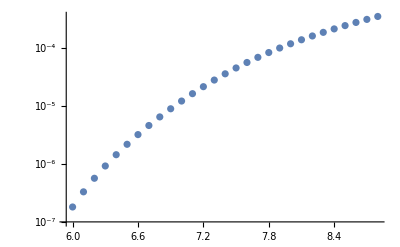

```mathematica
ListLogPlot[data]
```

0.9383

1.8756

0.197327

0.000510999

0.105658

0.197327

0.00729735

0.0611548

0.476519

-1.63718

1.08715

0.0593808

0.340761

0.622142

0.903522

0.0138977

0.0284999

-0.0539551

0.0115555

1.70073

1.17025

0.63978

0.109305

-0.16577

0.27557

-0.05382

-0.05598

0.0728354

0.582388

1.09194

1.60149

0.998132

25.8388

1.71397

-0.00170611

0.0141971

0.000081494

10.5814

10.8515

10.7721

10.7943

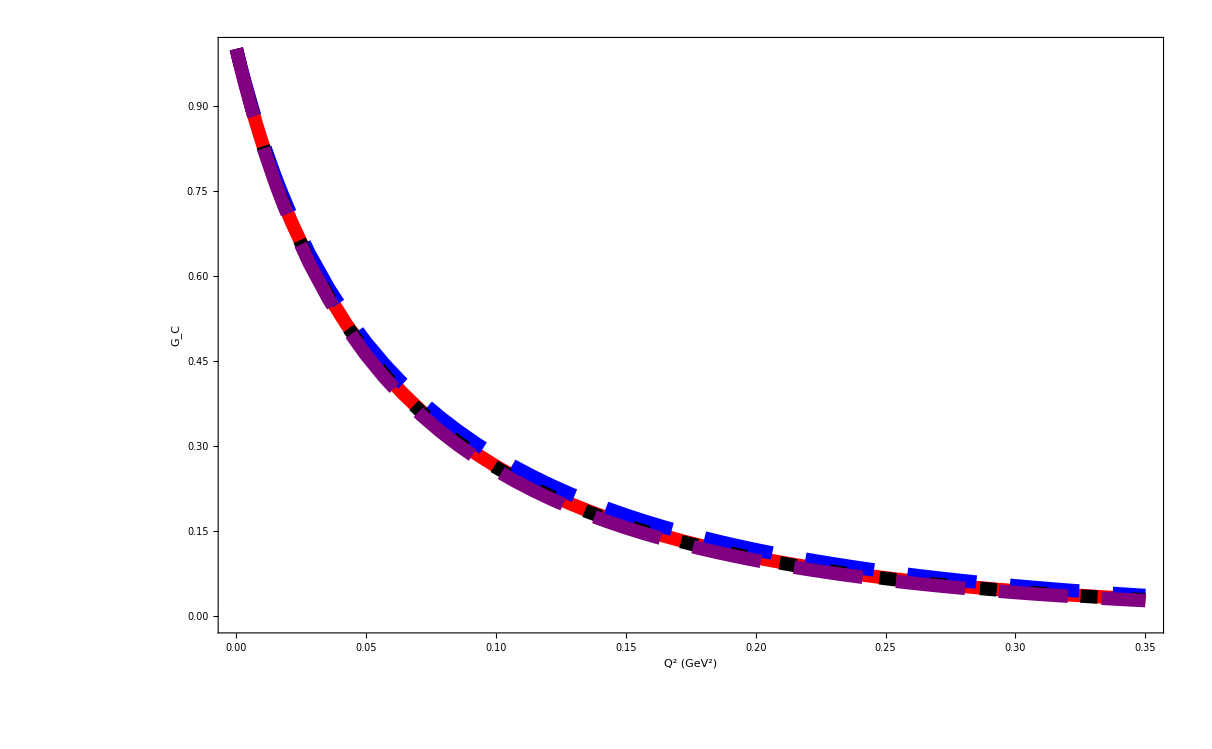

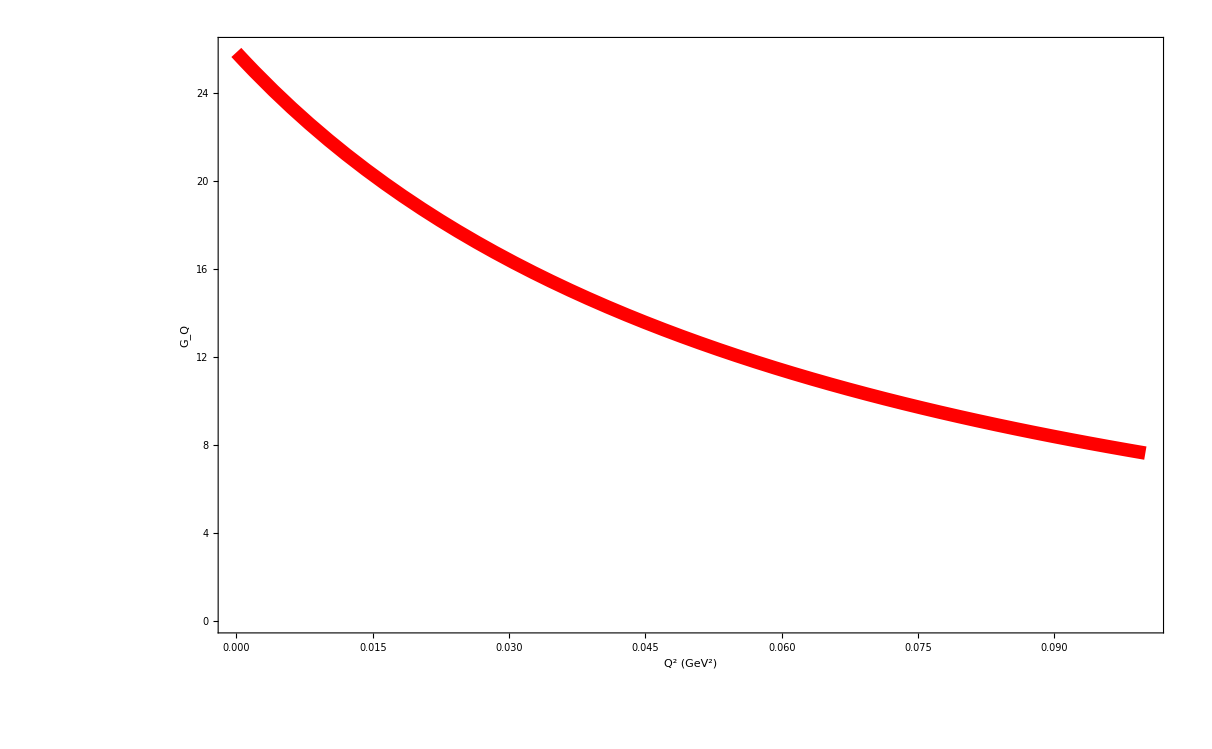

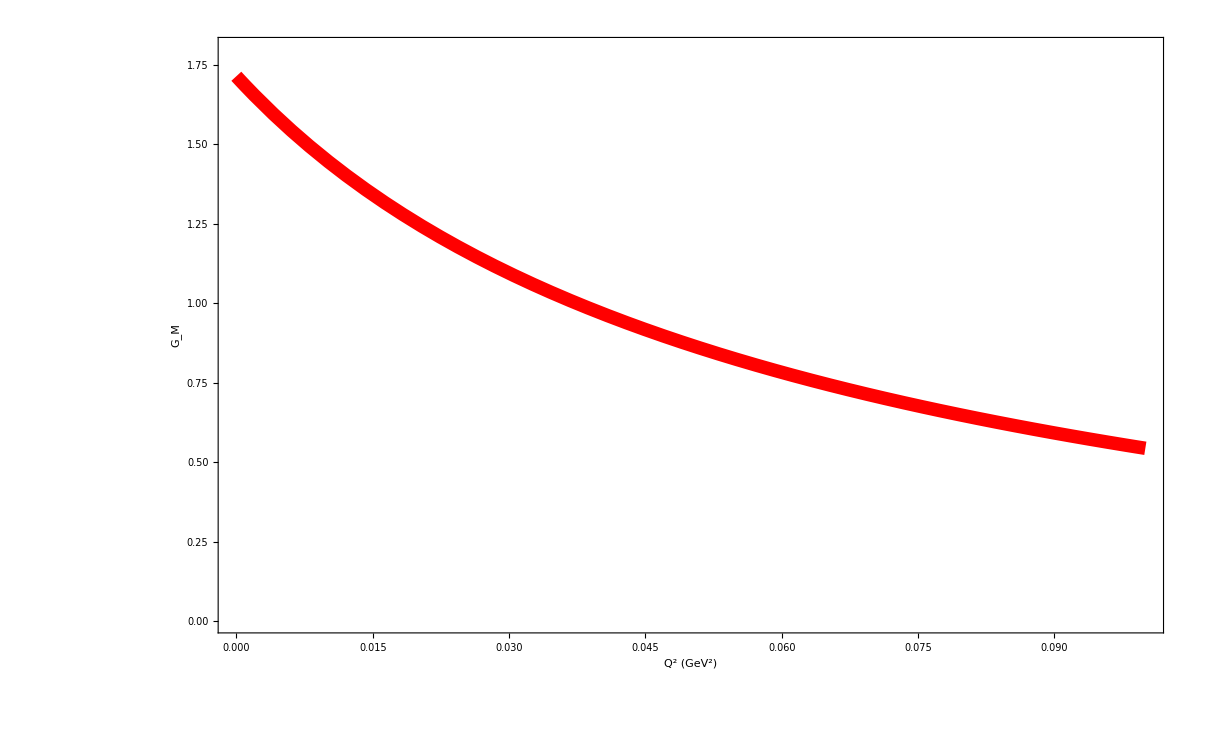

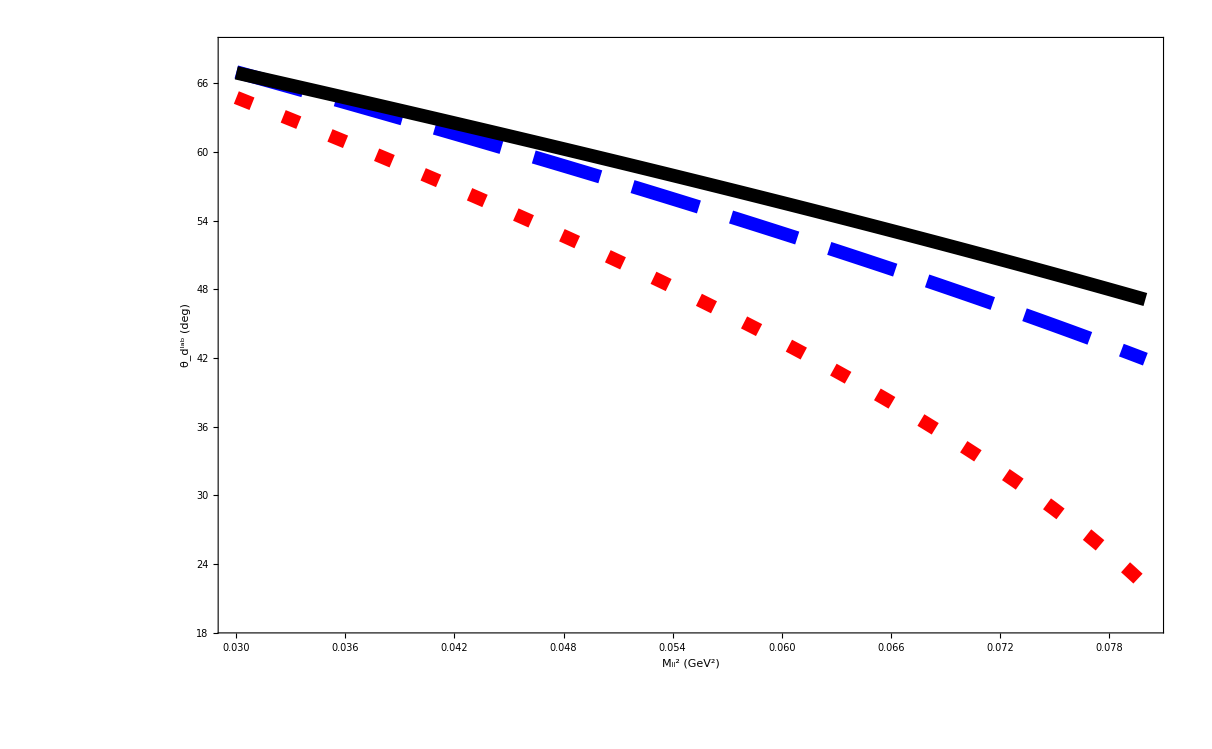

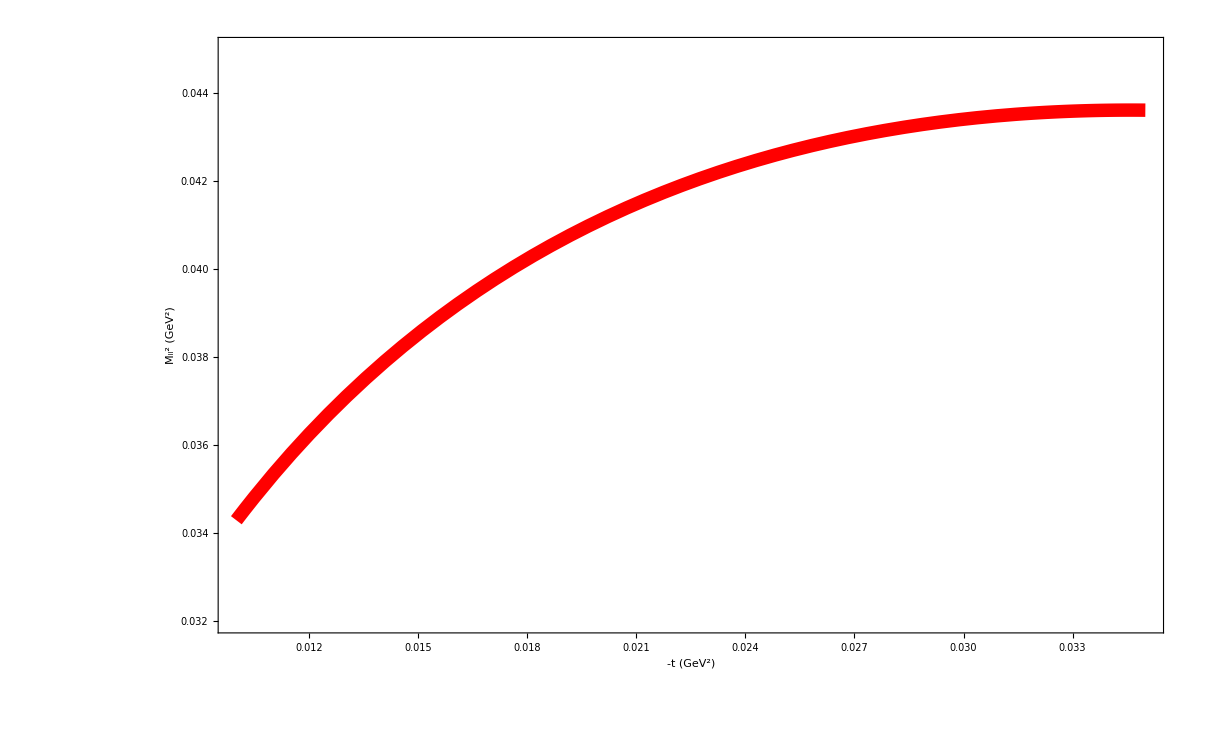

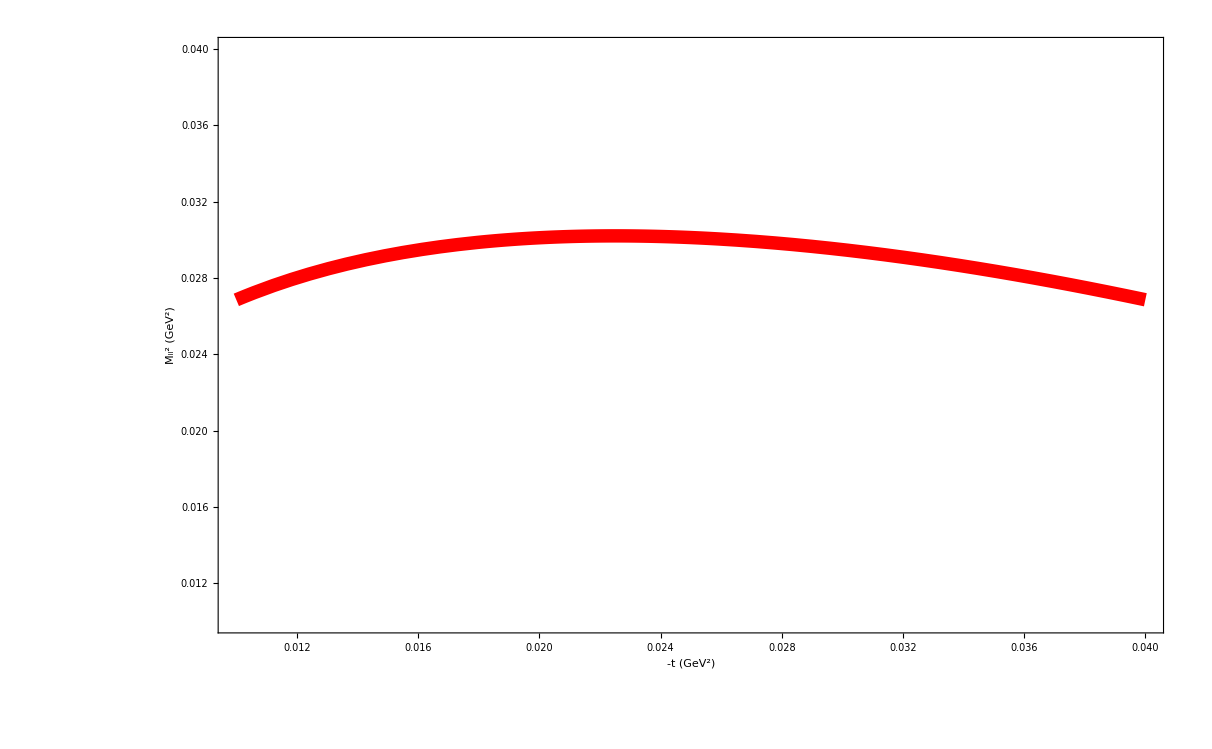

HERE18.5963

0.894531

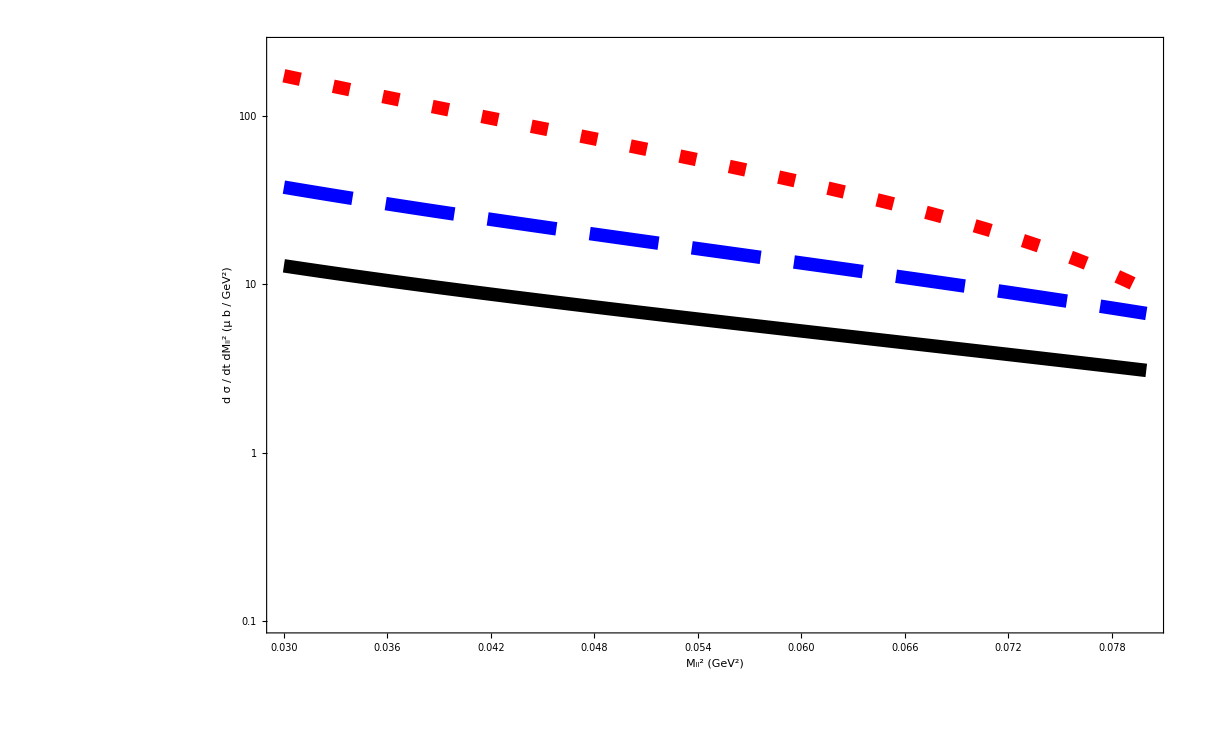

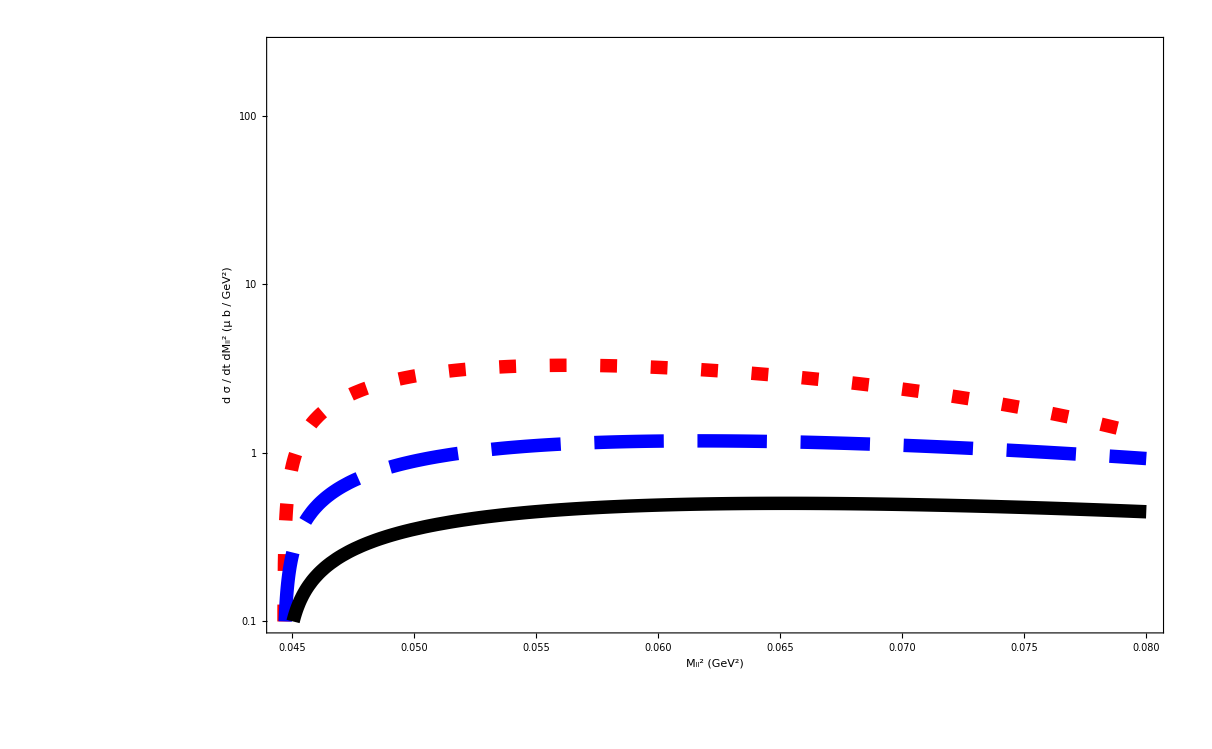

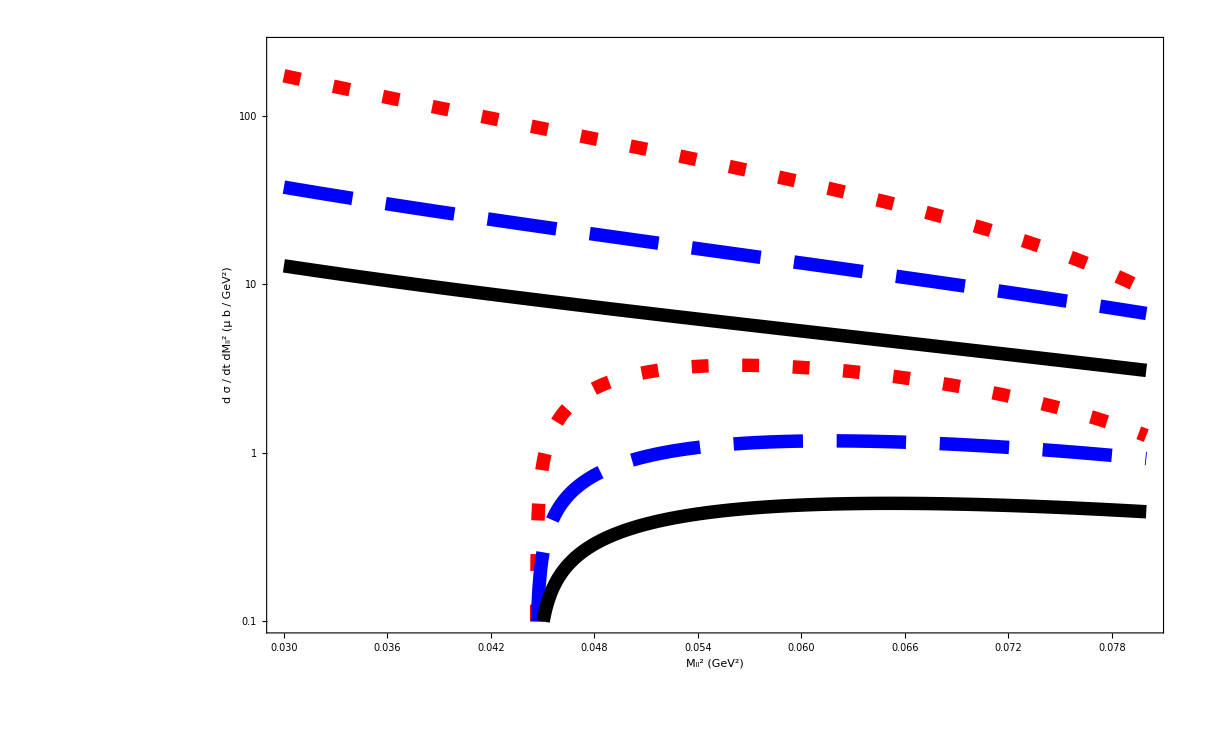

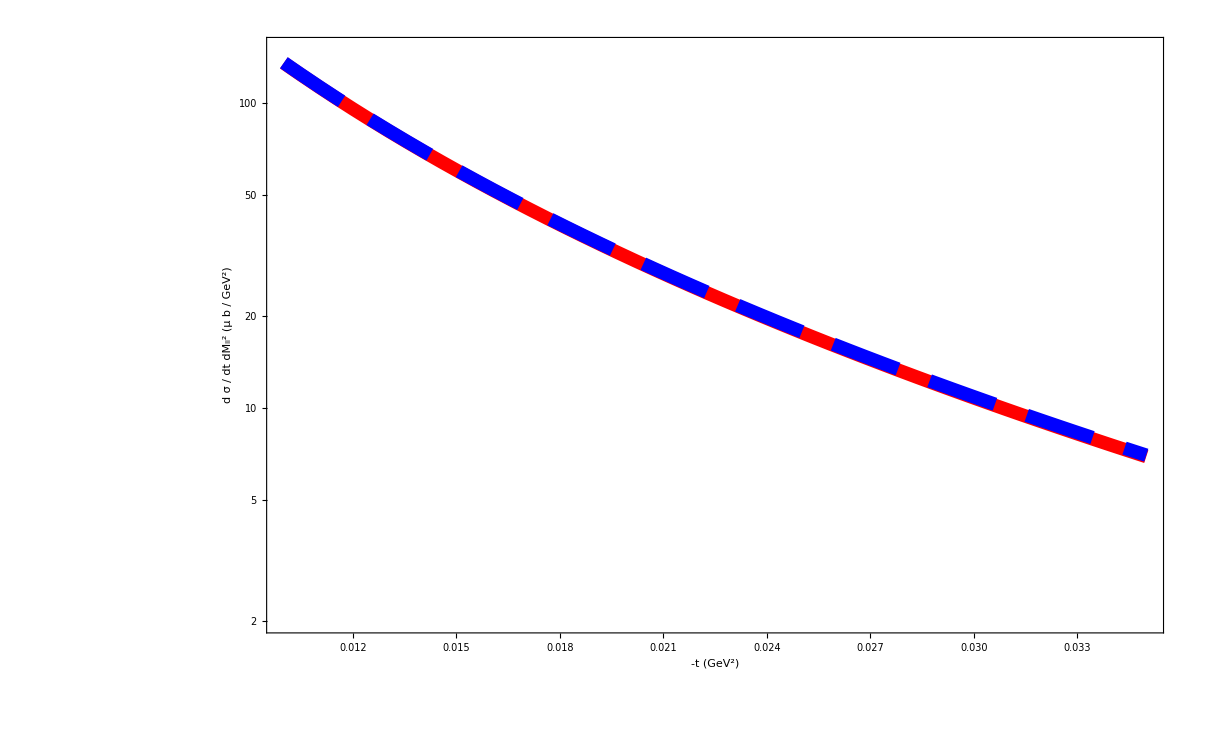

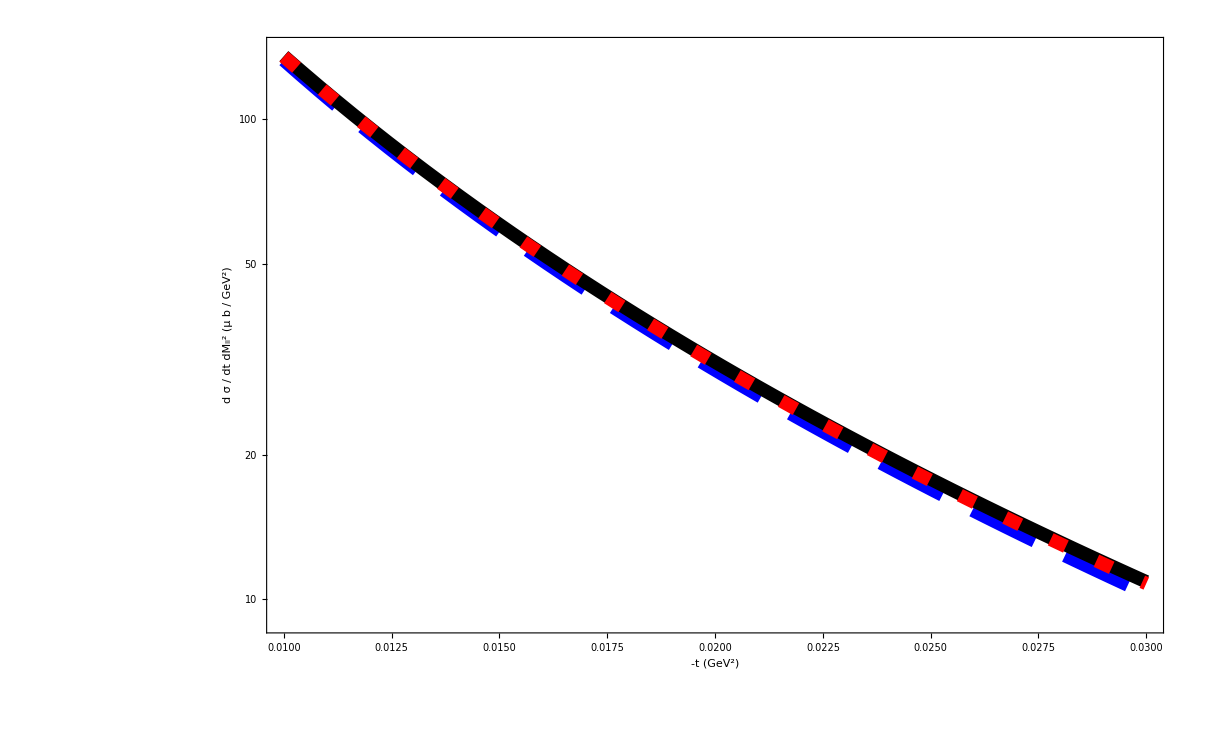

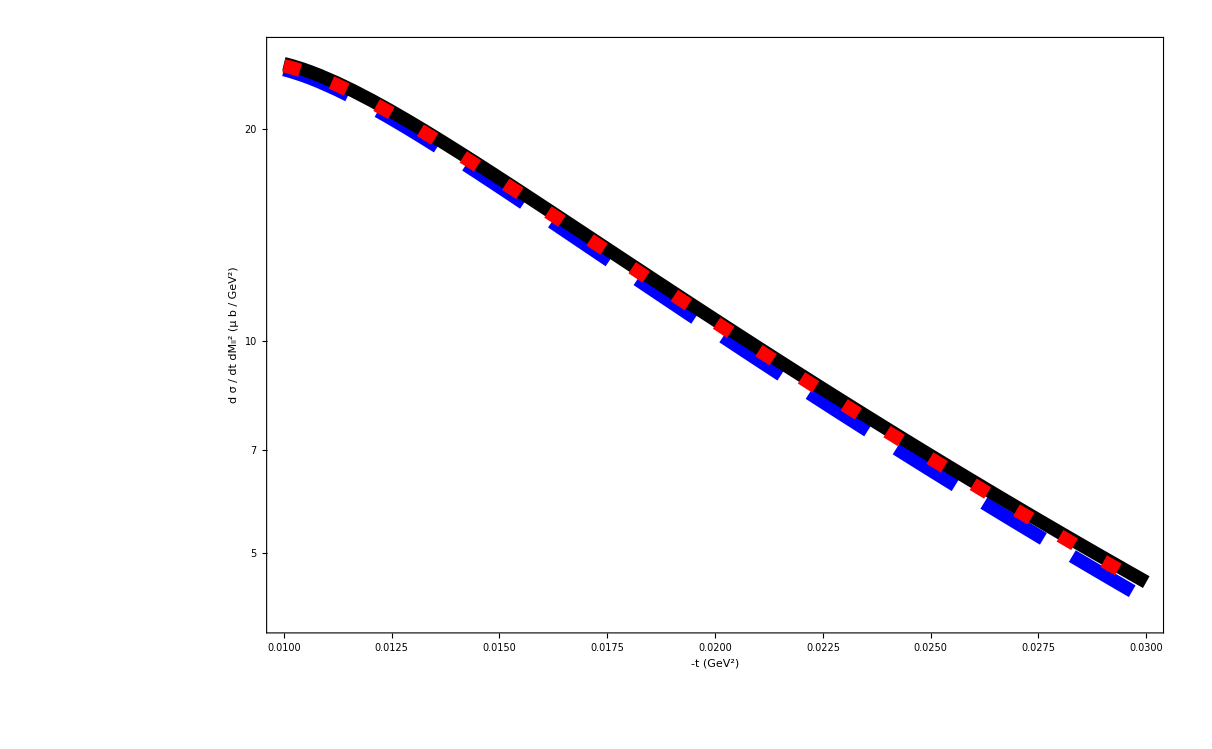

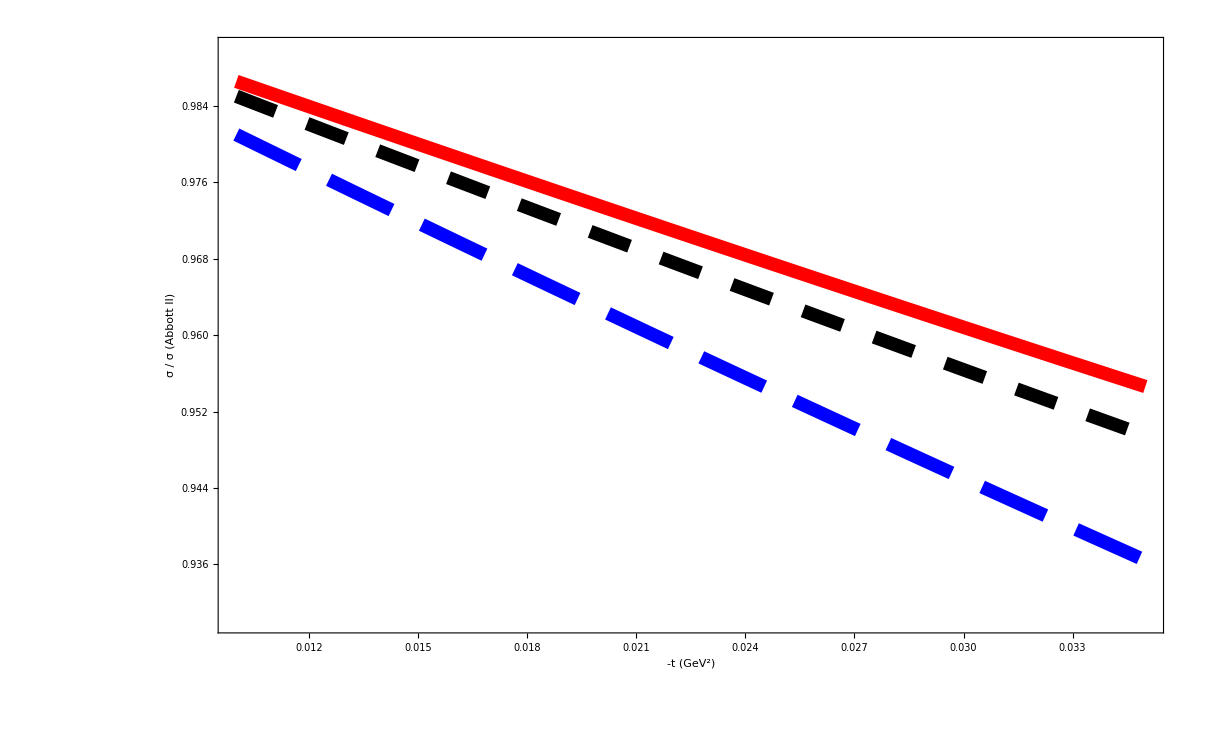

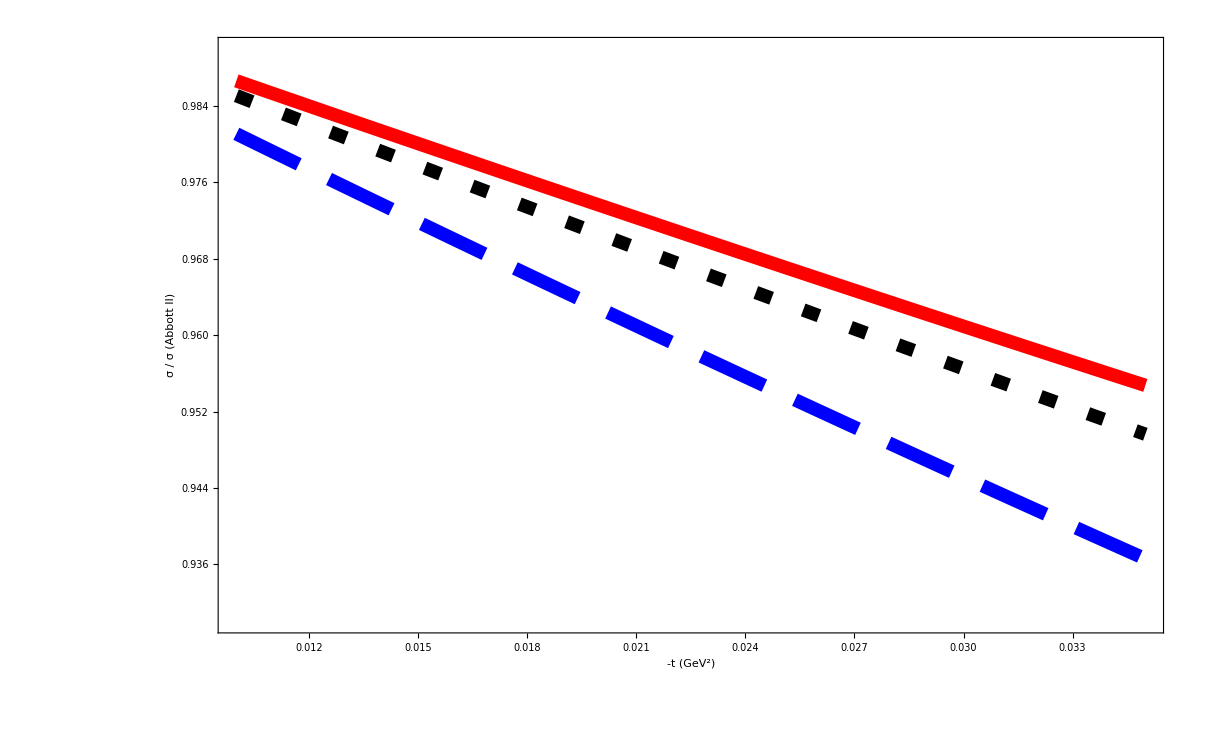

18.7833

1.56757

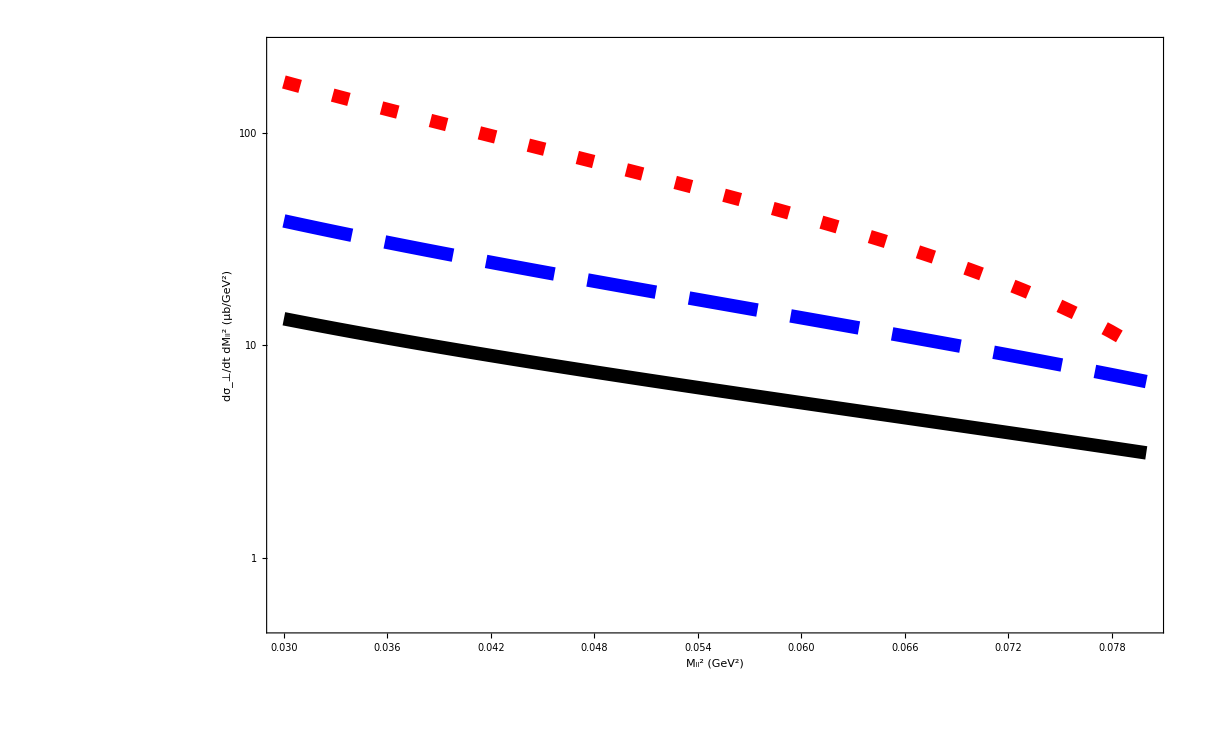

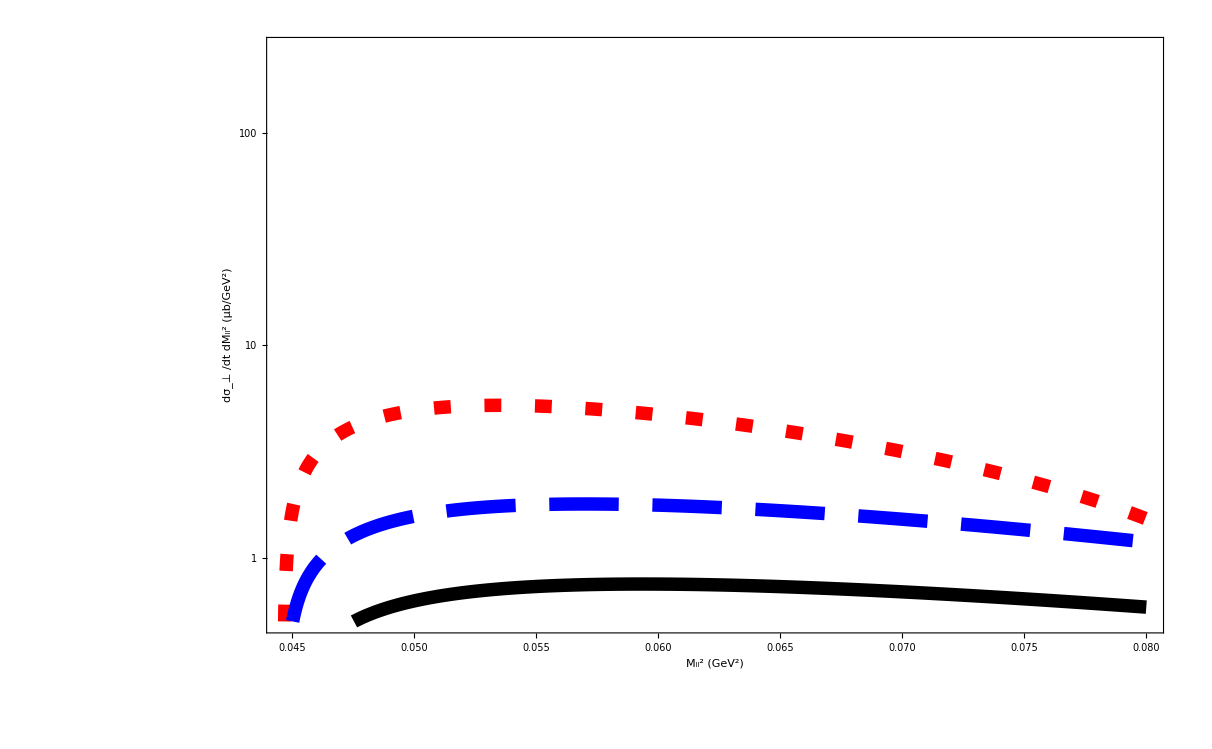

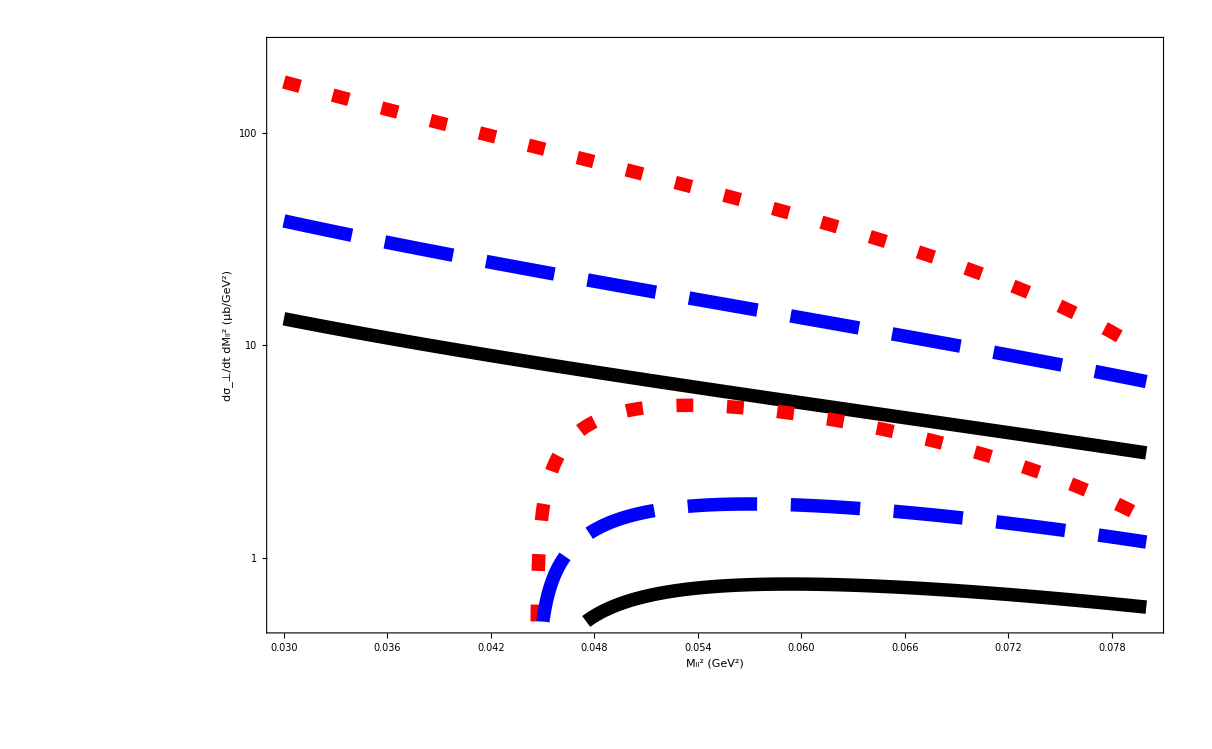

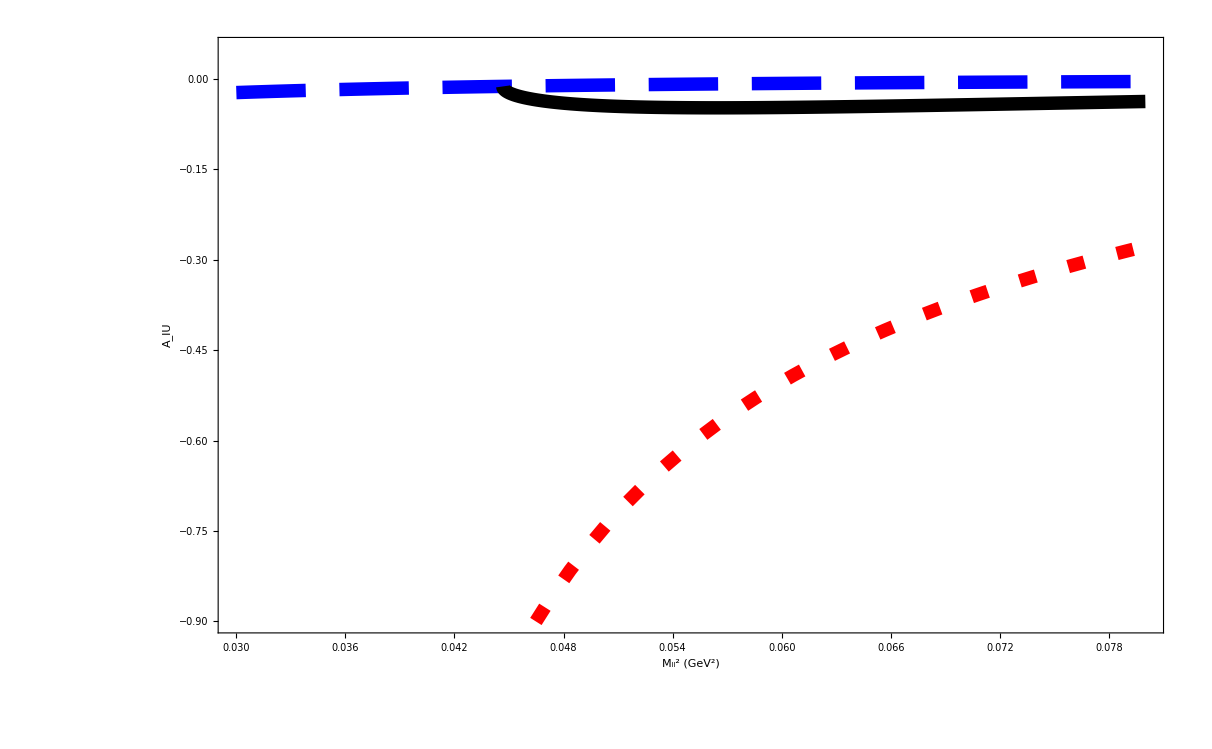

```mathematica
p1= LogPlot[{crossunpol[0.5,-0.01,Mllsqr,MELEC],crossunpol[0.5,-0.02,Mllsqr,MELEC],crossunpol[0.5,-0.03,Mllsqr,MELEC]},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "d σ / dt dM_ll^2  (μ b / GeV^2)"},PlotRange ->{0.1,250}]
p2= LogPlot[{crossunpol[0.5,-0.01,Mllsqr,MMUON],crossunpol[0.5,-0.02,Mllsqr,MMUON],crossunpol[0.5,-0.03,Mllsqr,MMUON]},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "d σ / dt dM_ll^2  (μ b / GeV^2)"},PlotRange ->{0.1,250}]
Show[p1,p2]


p3= LogPlot[{crossunpolC[0.5,-mt,0.035,MELEC],crossunpol[0.5,-mt,0.035,MELEC]},{mt, 0.01,0.035},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Dashing[{0.01,0.02}],Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "d σ / dt dM_ll^2  (μ b / GeV^2)"},PlotRange ->{2,150}]



p4= LogPlot[{crossunpolCCODATA[0.5,-mt,0.035,MELEC],crossunpol[0.5,-mt,0.035,MELEC],crossunpolC[0.5,-mt,0.035,MELEC]},{mt, 0.01,0.03},PlotStyle->{(*{Thickness[0.008],Red},*){Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black},{Dashing[{0.01,0.02}],Thickness[0.008],Red}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "d σ / dt dM_ll^2  (μ b / GeV^2)"},PlotRange ->{9,140}]

p5= LogPlot[{crossunpolCCODATA[0.5,-mt,0.07,MELEC]+crossunpolCCODATA[0.5,-mt,0.07,MMUON],crossunpol[0.5,-mt,0.07,MELEC]+crossunpol[0.5,-mt,0.07,MMUON],crossunpolC[0.5,-mt,0.07,MELEC]+crossunpolC[0.5,-mt,0.07,MMUON]},{mt, 0.01,0.03},PlotStyle->{(*{Thickness[0.008],Red},*){Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black},{Dashing[{0.01,0.02}],Thickness[0.008],Red}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "d σ / dt dM_ll^2  (μ b / GeV^2)"},PlotRange ->{4,26}]


p7= Plot[{crossunpolCpohl[0.5,-mt,0.035,MELEC]/crossunpol[0.5,-mt,0.035,MELEC],crossunpolCCODATA[0.5,-mt,0.035,MELEC]/crossunpol[0.5,-mt,0.035,MELEC],crossunpolCsick[0.5,-mt,0.035,MELEC]/crossunpol[0.5,-mt,0.035,MELEC]},{mt, 0.01,0.035},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Dashing[{0.025,0.02}],Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", " σ / σ (Abbott II)"},PlotRange ->{0.93,.99}]

p8= Plot[{(crossunpolCpohl[0.5,-mt,0.07,MELEC] +crossunpolCpohl[0.5,-mt,0.07,MMUON])/(crossunpol[0.5,-mt,0.07,MELEC] +crossunpol[0.5,-mt,0.07,MMUON]),(crossunpolCCODATA[0.5,-mt,0.07,MELEC]+crossunpolCCODATA[0.5,-mt,0.07,MMUON])/(crossunpol[0.5,-mt,0.07,MELEC] +crossunpol[0.5,-mt,0.07,MMUON]),(crossunpolCsick[0.5,-mt,0.07,MELEC]+crossunpolCsick[0.5,-mt,0.07,MMUON])/(crossunpol[0.5,-mt,0.07,MELEC] +crossunpol[0.5,-mt,0.07,MMUON])},{mt, 0.01,0.035},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Dashing[{0.01,0.02}],Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", " σ / σ (Abbott II)"},PlotRange ->{0.93,.99}]


p9= Plot[{ratiounpol[0.5,-mt,0.07]},{mt, 0.01,0.035},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Dashing[{0.01,0.02}],Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "σ (e^-e^+ + μ^-μ^+) / σ (e^-e^+)"},PlotRange ->{1.105,1.125}]


p10= Plot[{crossunpolCpohl[0.5,-0.02,Mllsqr,MELEC]/crossunpolCpohl[0.5,-0.01,Mllsqr,MELEC], crossunpolCCODATA[0.5,-0.02,Mllsqr,MELEC] /crossunpolCCODATA[0.5,-0.01,Mllsqr,MELEC],crossunpolCsick[0.5,-0.02,Mllsqr,MELEC] /crossunpolCsick[0.5,-0.01,Mllsqr,MELEC] },{Mllsqr, 0.03,0.042},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Dashing[{0.025,0.02}],Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "σ (-t = 0.02 GeV^2) / σ (-t = 0.01 GeV^2)"},PlotRange ->{0.21,.24}]

p11= Plot[{crossunpolCpohl[0.5,-0.03,Mllsqr,MELEC]/crossunpolCpohl[0.5,-0.02,Mllsqr,MELEC], crossunpolCCODATA[0.5,-0.03,Mllsqr,MELEC] /crossunpolCCODATA[0.5,-0.02,Mllsqr,MELEC],crossunpolCsick[0.5,-0.03,Mllsqr,MELEC] /crossunpolCsick[0.5,-0.02,Mllsqr,MELEC],
crossunpol[0.5,-0.03,Mllsqr,MELEC] /crossunpol[0.5,-0.02,Mllsqr,MELEC]},{Mllsqr, 0.03,0.042},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Dashing[{0.025,0.02}],Thickness[0.008],Black},{Dashing[{0.005,0.02}],Thickness[0.008],Purple}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "σ (-t = 0.03 GeV^2) / σ (-t = 0.02 GeV^2)"},PlotRange ->{0.333,.36}]

p12= Plot[{crossunpolCpohl[0.5,-0.035,Mllsqr,MELEC]/crossunpolCpohl[0.5,-0.02,Mllsqr,MELEC], crossunpolCCODATA[0.5,-0.035,Mllsqr,MELEC] /crossunpolCCODATA[0.5,-0.02,Mllsqr,MELEC],crossunpolCsick[0.5,-0.035,Mllsqr,MELEC] /crossunpolCsick[0.5,-0.02,Mllsqr,MELEC] },{Mllsqr, 0.03,0.042},PlotStyle->{{Thickness[0.008],Red},{Dashing[{0.1,0.02}],Thickness[0.008],Blue},{Dashing[{0.01,0.02}],Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "σ (-t = 0.035 GeV^2) / σ (-t = 0.02 GeV^2)"},PlotRange ->{0.21,.23}]


(* cross section with linear photon polarization perpendicular to the plane of the photon and recoiling proton *)

CE1perp[ega_,t_,Mllsqr_,lepm_]:= t (s[ega] - Md^2)(s[ega] - Md^2 - Mllsqr +t) (Mllsqr^2 + 6 Mllsqr t + 2 lepm^2 Mllsqr) + (Mllsqr - t)^2 Mllsqr (t^2  + Md^2 (Mllsqr + 2t) + 2 lepm^2 Md^2)
CE2perp[ega_,t_,Mllsqr_,lepm_]:= -t (s[ega] - Md^2)(s[ega] - Md^2 - Mllsqr +t) (Mllsqr^2 + t^2 + 4 lepm^2 (Mllsqr + t - lepm^2)) + (Mllsqr - t)^2 (- Md^2 (Mllsqr^2 + t^2) + 2 lepm^2 (- t^2 - 2 Md^2 (Mllsqr -t)+ 2 lepm^2 Md^2))
CEperp[ega_,t_,Mllsqr_,lepm_]:= CE1perp[ega,t,Mllsqr,lepm] + CE2perp[ega,t,Mllsqr,lepm] / beta[lepm,Mllsqr] * Log[(1 + beta[lepm,Mllsqr])/(1 - beta[lepm,Mllsqr])]

CM1perp[ega_,t_,Mllsqr_,lepm_]:= CE1perp[ega,t,Mllsqr,lepm] - 2 Md^2 (1 + tau[t])(Mllsqr - t)^2 (Mllsqr^2 + t^2 + 4 lepm^2 Mllsqr)
CM2perp[ega_,t_,Mllsqr_,lepm_]:= CE2perp[ega,t,Mllsqr,lepm] + 2 Md^2 (1 + tau[t])(Mllsqr - t)^2 (Mllsqr^2 + t^2 + 4 lepm^2 (Mllsqr - t - 2 lepm^2)) 
CMperp[ega_,t_,Mllsqr_,lepm_]:= CM1perp[ega,t,Mllsqr,lepm] + CM2perp[ega,t,Mllsqr,lepm] / beta[lepm,Mllsqr] * Log[(1 + beta[lepm,Mllsqr])/(1 - beta[lepm,Mllsqr])]


crossperp[ega_,t_,Mllsqr_,lepm_]:= conv^2 * 10^4 * ALPHAEM^3 / (s[ega] - Md^2)^2  * 4 beta[lepm,Mllsqr]/t^2 / (Mllsqr - t)^4 * 1/(1 + tau[t]) * (CEperp[ega,t,Mllsqr,lepm] * (GC[-t]^2 + 8/9 * tau[t]^2  * GQ[-t]^2) + CMperp[ega,t,Mllsqr,lepm] * 2/3 * tau[t] * GM[-t]^2)

crossperp[0.5,-0.02,0.05,MELEC]//N
crossperp[0.5,-0.02,0.05,MMUON]//N

p1b= LogPlot[{crossperp[0.5,-0.01,Mllsqr,MELEC],crossperp[0.5,-0.02,Mllsqr,MELEC],crossperp[0.5,-0.03,Mllsqr,MELEC]},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "dσ_⊥/dt dM_ll^2  (μb/GeV^2)"},PlotRange ->{0.5,250}]
p2b= LogPlot[{crossperp[0.5,-0.01,Mllsqr,MMUON],crossperp[0.5,-0.02,Mllsqr,MMUON],crossperp[0.5,-0.03,Mllsqr,MMUON]},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "dσ_⊥ /dt dM_ll^2  (μb/GeV^2)"},PlotRange ->{0.5,250}]
Show[p1b,p2b]

crosspar[ega_,t_,Mllsqr_,lepm_]:=2 crossunpol[ega,t,Mllsqr,lepm]- crossperp[ega,t,Mllsqr,lepm]
crossdiff[ega_,t_,Mllsqr_,lepm_]:=crosspar[ega,t,Mllsqr,lepm]- crossperp[ega,t,Mllsqr,lepm]
photonasymm[ega_,t_,Mllsqr_,lepm_]:=crossdiff[ega,t,Mllsqr,lepm]/(2 crossunpol[ega,t,Mllsqr,lepm])

p3b= Plot[{photonasymm[0.5,-0.02,Mllsqr,MMUON],photonasymm[0.5,-0.02,Mllsqr,MELEC],(crossdiff[0.5,-0.02,Mllsqr,MELEC] + crossdiff[0.5,-0.02,Mllsqr,MMUON])/2/(crossunpol[0.5,-0.02,Mllsqr,MELEC] + crossunpol[0.5,-0.02,Mllsqr,MMUON])},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.01,0.02}],Thickness[0.008],Red},{Dashing[{0.05,0.02}],Thickness[0.008],Blue},{Thickness[0.008],Black}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "A_lU  "},PlotRange ->{-0.9,0.05}]
```

0.938272

0.000510999

0.105658

0.197327

0.00729735

0.134977

(√(0.743278-1.79715 s+s^2))/(2 √s)

1.34856

0.328289

0.354954

20.8757

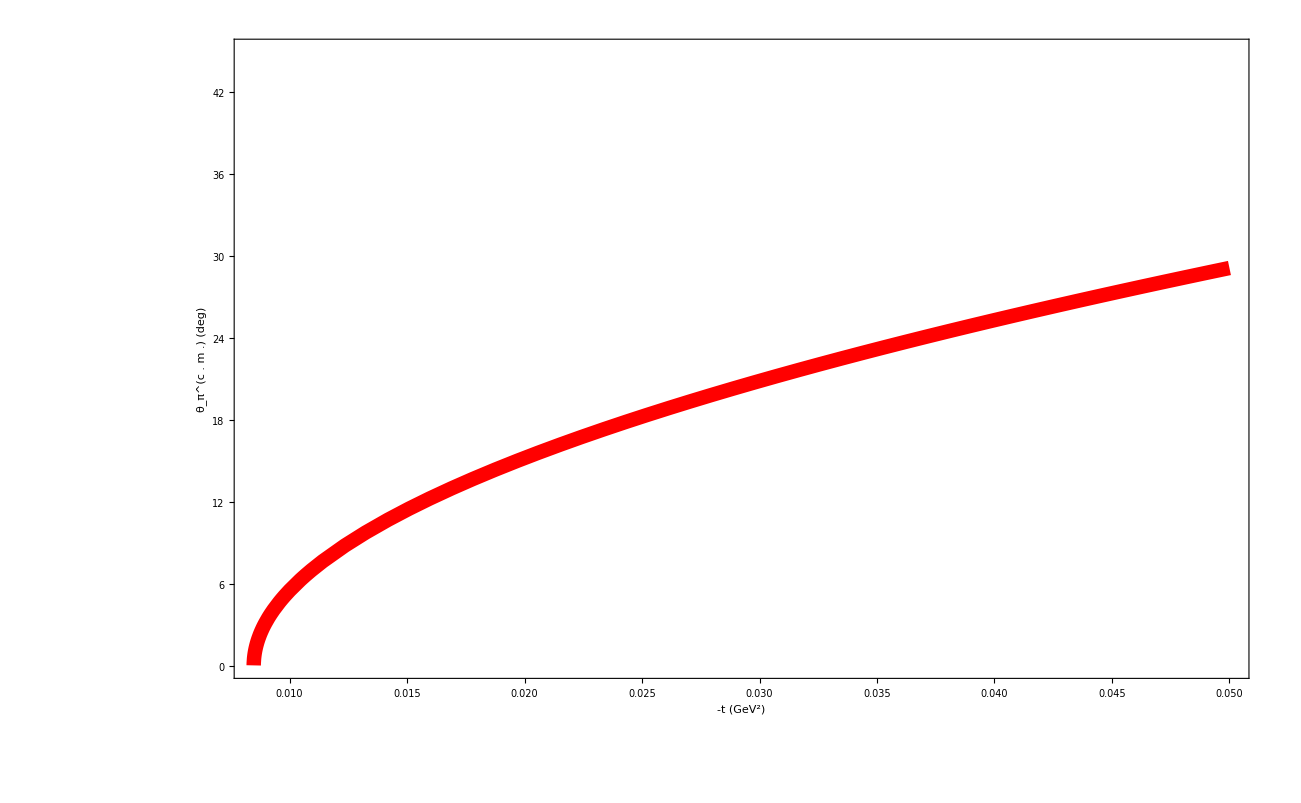

18.7921

0.00377992

13.3068

0.00754701

10.8803

0.0113014

0.0301636

0.0624624

0.097444

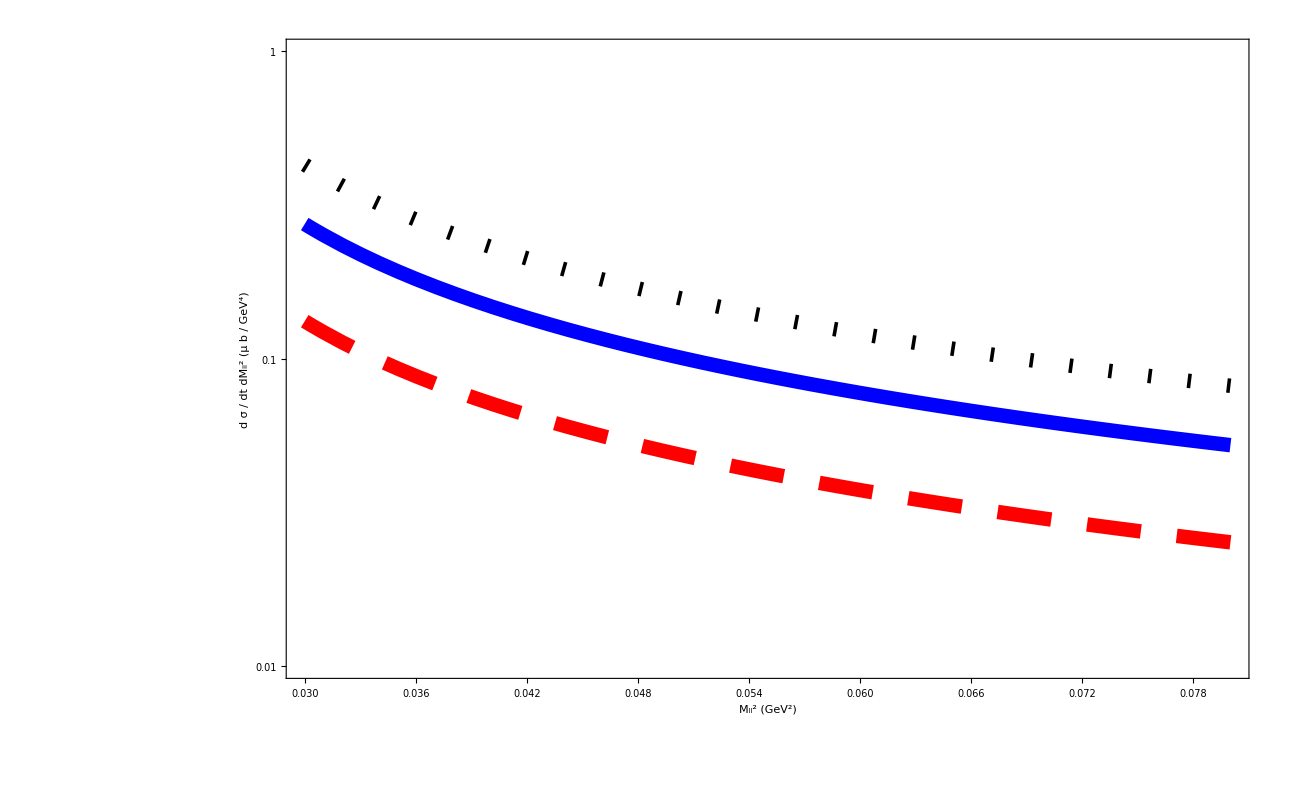

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];
SetOptions[LogPlot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];
SetOptions[LogLinearPlot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];
SetOptions[ContourPlot,BaseStyle->{FontFamily->"TimesNewRoman",FontSize->30, FontWeight -> "Bold",FontSlant -> "Italic"}];

M = 0.938272
MELEC = 0.000510999
MMUON = 0.105658
hbarc = 0.197327
ALPHAEM = 1/137.036
mpi = 0.1349766

lambdapi[s_]:= s^2  + M^4 + mpi^4 - 2 M ^2mpi^2 - 2 s mpi^2 - 2 s M^2 
pi0mom[s_] = Sqrt[lambdapi[s]] / (2 Sqrt[s])
pi0en[s_]:= Sqrt[pi0mom[s]^2 + mpi^2]
sinv[ega_]:= M^2 + 2 M ega
Sqrt[sinv[0.5]]//N

pi0mom[1.349^2]//N
pi0en[1.349^2]//N

costhpi[ega_,t_]:= (t - mpi^2 + 2 ega * pi0en[sinv[ega]])/(2 ega * pi0mom[sinv[ega]])
ArcCos[costhpi[.5,-0.03]]* 180/Pi//N

Plot[{ArcCos[costhpi[0.5,-mt]] * 180/Pi},{mt, 0.005,0.05},PlotStyle->{{Thickness[0.008],Red}},
Frame->{True,True,False,False},FrameLabel ->{"-t  (GeV^2)", "θ_π^(c . m .) (deg)"},PlotRange ->{0,45}]

W[v_]:= -1 + (v^2 + 1)/(2 v) * Log[(v+1)/(v-1)]
vrel[t_]:= Sqrt[1 - 4 M^2/t]
sigmapi0[ega_,t_]:= 3.5

vrel[-0.01]//N
W[vrel[-0.01]]//N
vrel[-0.02]//N
W[vrel[-0.02]]//N
vrel[-0.03]//N
W[vrel[-0.03]]//N

crosspi0gamma[ega_,t_,Mllsqr_]:= 1/(Mllsqr - mpi^2) * ALPHAEM * 4/Pi  sinv[ega]/ (sinv[ega] - M^2) /   Sqrt[lambdapi[sinv[ega]]] * W[vrel[t]] * 2 * Pi 
crosspi0gamma[.5,-0.01,0.07]* 3.23//N
crosspi0gamma[.5,-0.02,0.07]*3.35//N
crosspi0gamma[.5,-0.03,0.07]*3.49//N

LogPlot[{crosspi0gamma[0.5,-0.01,Mllsqr] * 3.23,crosspi0gamma[0.5,-0.03,Mllsqr] * 3.49,crosspi0gamma[0.5,-0.02,Mllsqr] * 3.35},{Mllsqr, 0.03,0.08},PlotStyle->{{Dashing[{0.03,0.02}],Thickness[0.008],Red},{Dashing[{0.002,0.02}],Thickness[0.008],Black},{Thickness[0.008],Blue}},
Frame->{True,True,False,False},FrameLabel ->{"M_ll^2  (GeV^2)", "d σ / dt dM_ll^2  (μ b / GeV^4)"},PlotRange ->{0.01,1}]
```

```mathematica
g1 = (1 + tau) (gc - 2/3 tau gq)
g3 = gm - gc + (1 + 2/3 tau) gq

test = 2 g1*g1 + 4 g1 * g3 tau (1 + 2 tau) + 4 tau^2 (1 + 2 tau) g3*g3 - 8 tau^2 (1 + tau) gm * g3 + 2 tau (1 + tau)^2 gm*gm + (1 + 2 tau)^2 g1^2 - 4 tau (1 + 2 tau) (1 + tau) g1 * gm + 4 tau^2 (1 + tau)^2 gm*gm+ 4 tau^2 (1 + 2 tau) g1 * g3 + 4 tau^4 g3*g3 - 8 tau^3 (1 + tau) gm * g3

Simplify[test]
```

(1+tau) (gc-(2 gq tau)/3)

-gc+gm+gq (1+(2 tau)/3)

4 (-gc+gm+gq (1+(2 tau)/3))^2 tau^4-8 gm (-gc+gm+gq (1+(2 tau)/3)) tau^2 (1+tau)-8 gm (-gc+gm+gq (1+(2 tau)/3)) tau^3 (1+tau)+2 gm^2 tau (1+tau)^2+4 gm^2 tau^2 (1+tau)^2+4 (-gc+gm+gq (1+(2 tau)/3))^2 tau^2 (1+2 tau)+4 (-gc+gm+gq (1+(2 tau)/3)) tau (1+tau) (1+2 tau) (gc-(2 gq tau)/3)+4 (-gc+gm+gq (1+(2 tau)/3)) tau^2 (1+tau) (1+2 tau) (gc-(2 gq tau)/3)-4 gm tau (1+tau)^2 (1+2 tau) (gc-(2 gq tau)/3)+2 (1+tau)^2 (gc-(2 gq tau)/3)^2+(1+tau)^2 (1+2 tau)^2 (gc-(2 gq tau)/3)^2

1/3 (1+tau)^2 (9 gc^2+6 gm^2 tau+8 gq^2 tau^2)

```mathematica
Series[(1 - ao x + b x^2 + c x^3)/(1 +(an - ao)x (1 + an x)), {x,0,3}]
```

1-an x+b x^2+(an^3-an^2 ao-an b+ao b+c) x^3+O[x]^4

```mathematica
crossunpol[0.5,-0.02,0.05,MELEC]//N
```

```mathematica
Print["HERE",crossunpol[0.5,-0.02,0.05,MELEC]//N]
```